```mathematica
Int[n1_,n2_]:=Abs[Sign[n1-n2]] π √(n1*n2)SeriesCoefficient[-1/(2 π^2)PolyGamma[ⅈ/(2 π) Log[(1+x)/(1-x)]+ⅈ/(2 π)Log[ (1+y)/(1-y)]+1/2],{x,0,n1/2},{y,0,n2/2}]
Diag[n1_]:= π n1*SeriesCoefficient[-1/(2 π^2)PolyGamma[ⅈ/(2 π) Log[(1+x)/(1-x)]+ⅈ/(2 π)Log[ (1+y)/(1-y)]+1/2],{x,0,n1/2},{y,0,n1/2}]
degen[v_]:=Table[Length[Split[Sort[v]][[i]]],{i,1,Length[Split[Sort[v]]]}]
w[v_]:=Table[Split[Sort[v]][[i]][[1]],{i,1,Length[Split[Sort[v]]]}];
c[v_]:=Table[Diag[w[v][[i]]],{i,1,Length[w[v]]}]
IPartBase[v_]:=Product[1/((degen[v][[i]]-1)!),{i,1,Length[w[v]]}]Sum[ⅇ^(ⅈ*d[[i]]*x)Product[1/(d[[i]]-d[[j]]),{j,1,i-1}]* Product[1/(d[[i]]-d[[j]]),{j,i+1,Length[w[v]]}],{i,1,Length[w[v]]}];
IPartDer[v_]:=Fold[D[#1,#2]&,IPartBase[v],Table[{d[[i]],degen[v][[i]]-1},{i,1,Length[w[v]]}]];
IPart[v_,c_]:=Evaluate[IPartDer[v]]/.d->c
Amplitude[v_]:=Product[Int[v[[i]],v[[i+1]]],{i,1,Length[v]-1}]*IPart[v,c[v]]
```

```mathematica
a0=Amplitude[{4}]
```

ⅇ^(-(ⅈ x PolyGamma[4,1/2])/(2 π^5))

```mathematica
a2[vmax_]:=Sum[Amplitude[{4,v1,4}],{v1,4,vmax,4}];
```

```mathematica
a3[vmax1_,vmax2_]:=Sum[Amplitude[{4,v1,v2,4}],{v1,4,vmax1,4},{v2,4,vmax2,4}];
```

```mathematica
a4[vmax1_,vmax2_]:=Sum[Amplitude[{4,v1,v2,v3,4}],{v1,4,vmax1,4},{v2,4,vmax2,4},{v3,4,vmax1,4}];
```

```mathematica
a5[vmax1_,vmax2_]:=Sum[Amplitude[{4,v1,v2,v3,v4,4}],{v1,4,vmax1,4},{v2,4,vmax2,4},{v3,4,vmax2,4},{v4,4,vmax1,4}];
```

```mathematica
a6[vmax1_,vmax2_,vmax3_]:=Sum[Amplitude[{4,v1,v2,v3,v4,v5,4}],{v1,4,vmax1,4},{v2,4,vmax2,4},{v3,4,vmax3,4},{v4,4,vmax2,4},{v5,4,vmax1,4}];
```

```mathematica
a7[vmax1_,vmax2_,vmax3_]:=Sum[Amplitude[{4,v1,v2,v3,v4,v5,v6,4}],{v1,4,vmax1,4},{v2,4,vmax2,4},{v3,4,vmax3,4},{v4,4,vmax3,4},{v5,4,vmax2,4},{v6,4,vmax1,4}];
```

```mathematica
a8=Sum[Amplitude[{4,v1,v2,v3,v4,v5,v6,4}],{v1,4,12,4},{v2,4,16,4},{v3,4,20,4},{v4,4,24,4},{v5,4,20,4},{v6,4,16,4},{v7,4,12,4}];
```

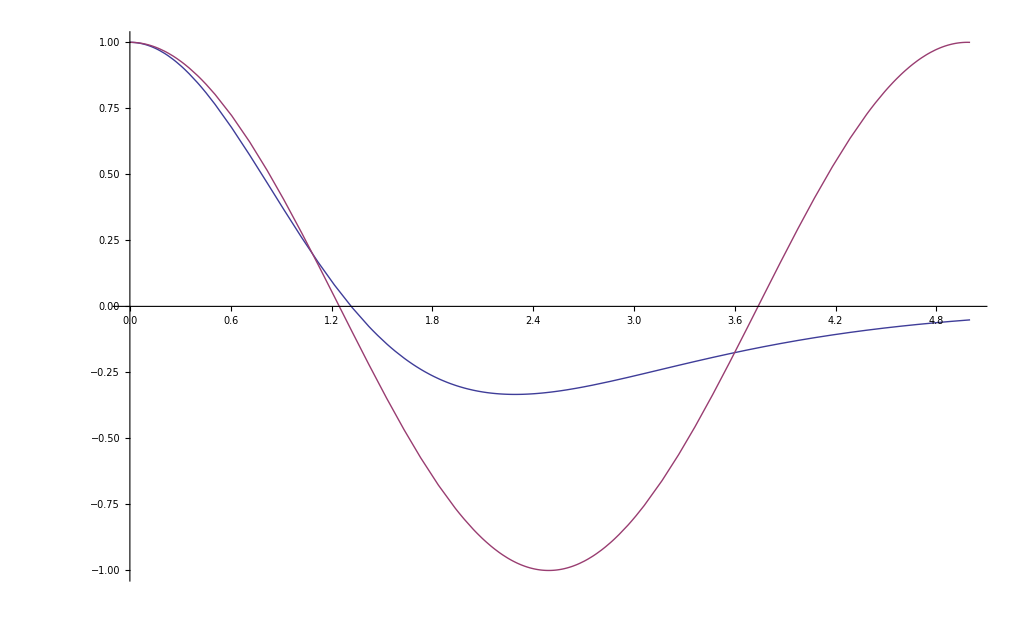

```mathematica
Plot[{2*4*NIntegrate[Re[ⅇ^(ⅈ *x* k)1/(k Sinh[k*π])k^4],{k,0,100}],Re[a0]},{x,0,5}]
```

```mathematica
a2approx1=a2[20];
```

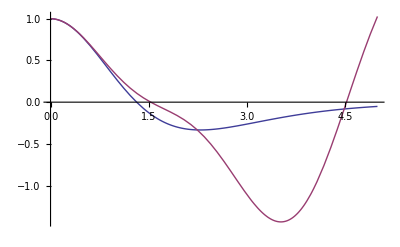

```mathematica
Plot[{2*4*NIntegrate[Re[ⅇ^(ⅈ *x* k)1/(k Sinh[k*π])k^4],{k,0,100}],Re[a0+a2approx1]},{x,0,5}]
```

```mathematica
Base1=a0+a2approx1;
```

```mathematica
Graphically analyzing convergence of m=3 term
```

```mathematica
a3approx1=a3[12,12];
```

```mathematica
a3approx2=a3[20,20];
```

```mathematica
a3approx3=a3[40,40];
```

```mathematica
a3approx4=a3[80,80];
```

```mathematica
a3approx5=a3[200,200];
```

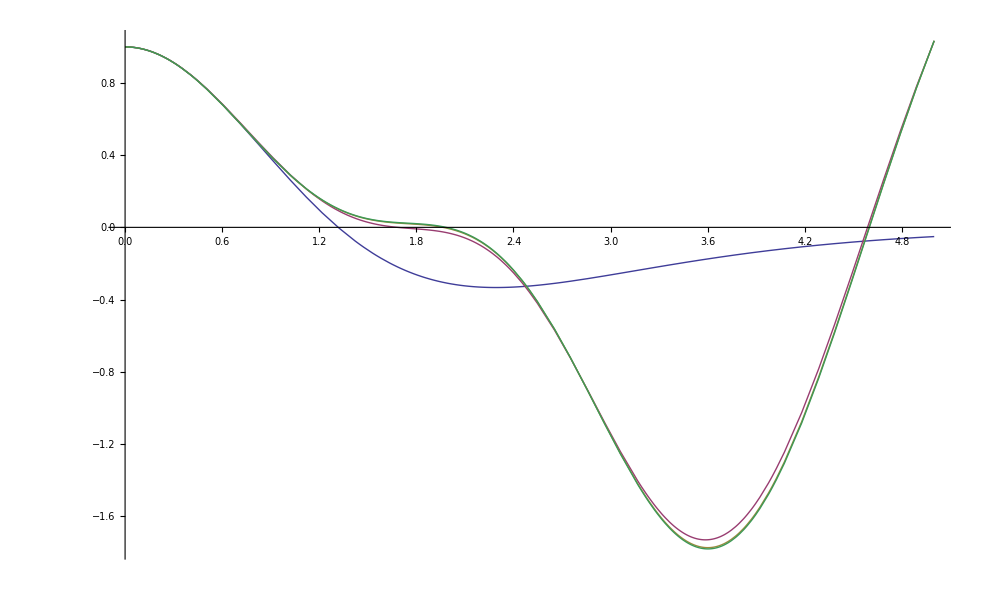

```mathematica
Plot[{2*4*NIntegrate[Re[ⅇ^(ⅈ *x* k)1/(k Sinh[k*π])k^4],{k,0,100}],Re[Base1+a3approx1],Re[Base1+a3approx2],Re[Base1+a3approx3]},{x,0,5}]
```

```mathematica
Base2=Base1+a3approx3;
```

```mathematica
Graphically analyzing convergence of m=4 term.
```

```mathematica
a4approx1=a4[12,16];
```

```mathematica
a4approx2=a4[20,24];
```

```mathematica
a4approx3=a4[24,28];
```

```mathematica
a4approx4=a4[48,52];
```

```mathematica
a4approx4=a4[100,100];
```

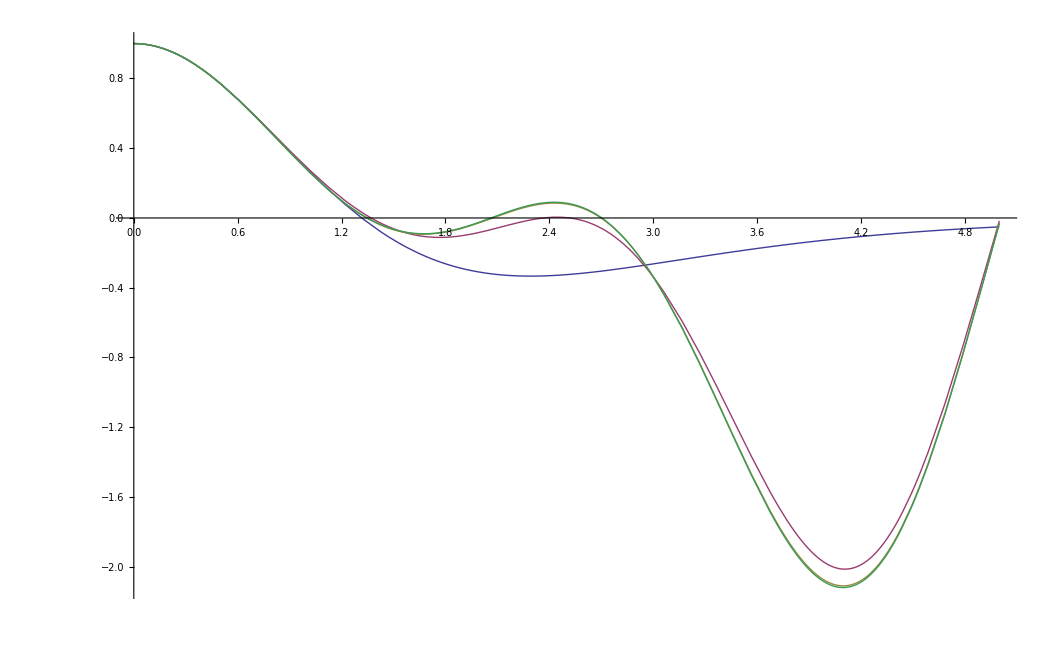

```mathematica
Plot[{2*4*NIntegrate[Re[ⅇ^(ⅈ *x* k)1/(k Sinh[k*π])k^4],{k,0,100}],Re[Base2+a4approx1],Re[Base2+a4approx2],Re[Base2+a4approx3]},{x,0,5}]
```

```mathematica
aBase3=Base2+a4approx2;
```

```mathematica
a5approx1=a5[12,16];
```

```mathematica
a5approx2=a5[20,24];
```

```mathematica
a5approx3=a5[28,32];
```

```mathematica
a5approx4=a5[40,44];
```

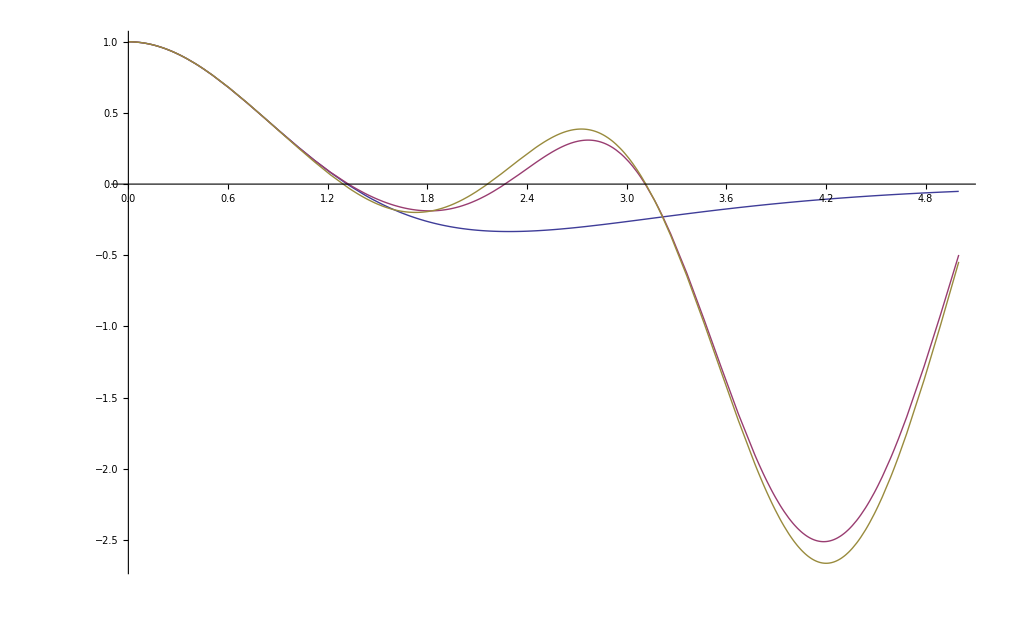

```mathematica
Plot[{2*4*NIntegrate[Re[ⅇ^(ⅈ *x* k)1/(k Sinh[k*π])k^4],{k,0,100}],Re[aBase3+a5approx1],Re[aBase3+a5approx2]},{x,0,5}]
```

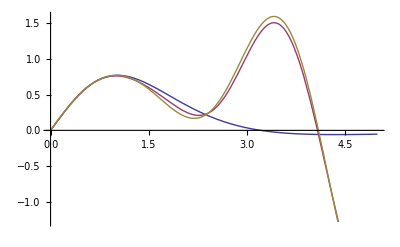

```mathematica
Plot[{2*4*NIntegrate[Im[ⅇ^(ⅈ *x* k)1/(k Sinh[k*π])k^4],{k,0,100}],Im[aBase3+a5approx1],Im[aBase3+a5approx2]},{x,0,5}]
```

```mathematica
aBase4=aBase3+a5approx4;
```

```mathematica
Compare m=6
```

```mathematica
a6approx1=a6[8,12,16];
```

```mathematica
a6approx2=a6[12,16,20];
```

```mathematica
a6approx3=a6[16,20,24];
```

```mathematica
a6approx4=a6[20,24,28];
```

```mathematica
a6approx5=a6[24,28,32];
```

```mathematica
a7approx6=a6[32,36,40];
```

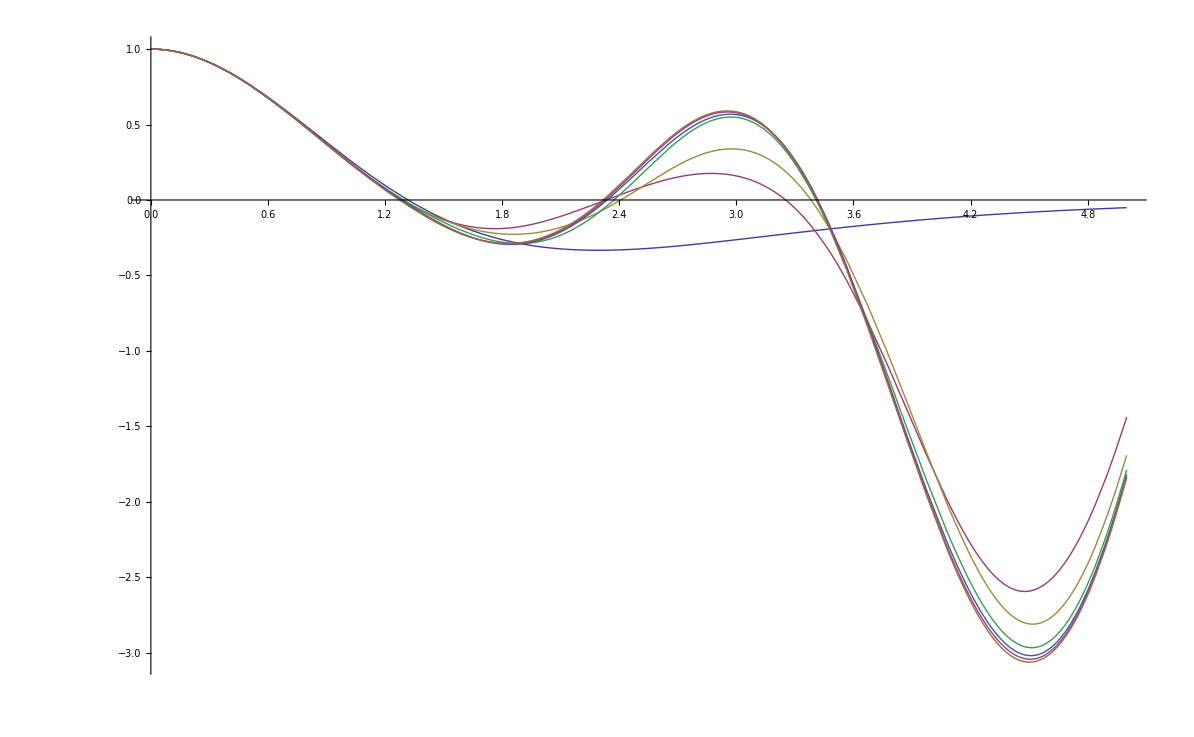

```mathematica
Plot[{2*4*NIntegrate[Re[ⅇ^(ⅈ *x* k)1/(k Sinh[k*π])k^4],{k,0,100}],Re[aBase4+a6approx1],Re[aBase4+a6approx2],Re[aBase4+a6approx3],Re[aBase4+a6approx4],Re[aBase4+a6approx5],Re[aBase4+a7approx6]},{x,0,5}]
```

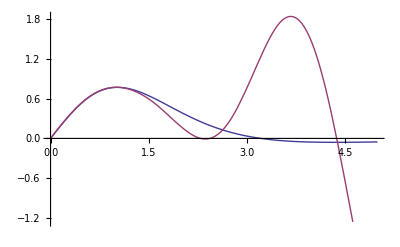

```mathematica
Plot[{2*4*NIntegrate[Im[ⅇ^(ⅈ *x* k)1/(k Sinh[k*π])k^4],{k,0,100}],Im[aBase5]},{x,0,5}]
```

```mathematica
aBase5=aBase4+a7approx6;
```

```mathematica
a7approx1=a7[12,16,20];
```

```mathematica
a7approx2=a7[20,24,28];
```

```mathematica
a7approx3=a7[28,32,36];
```

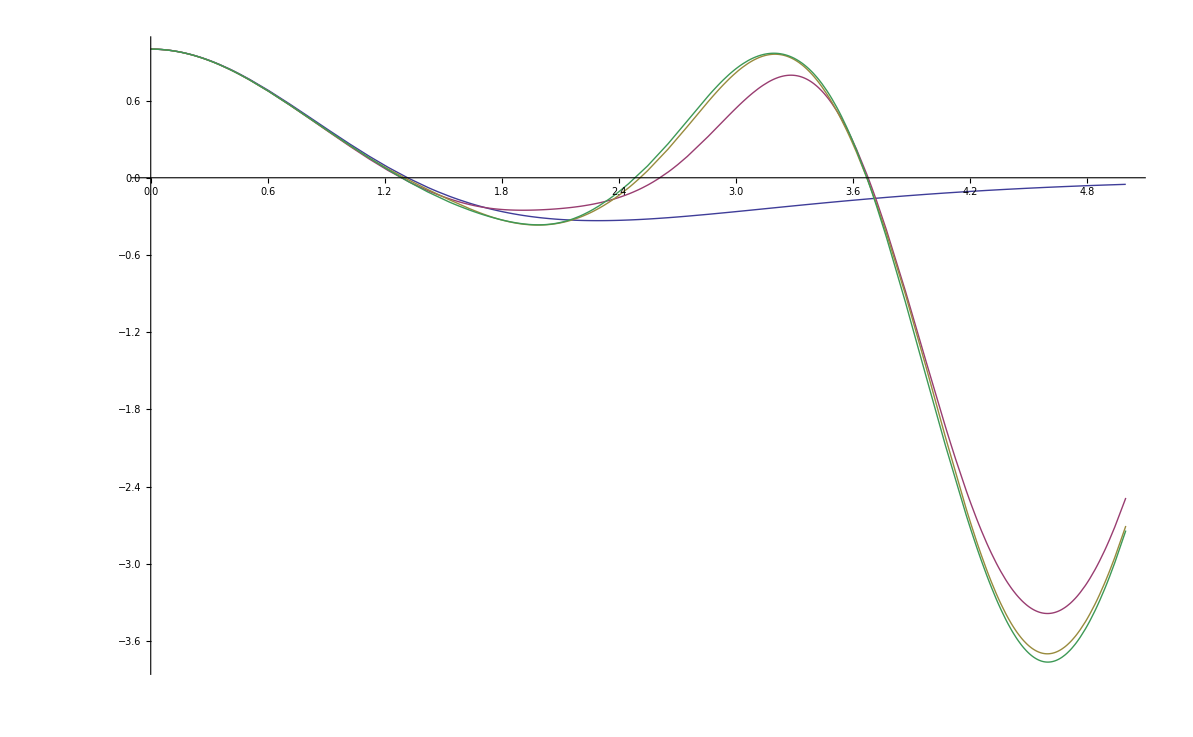

```mathematica
Plot[{2*4*NIntegrate[Re[ⅇ^(ⅈ *x* k)1/(k Sinh[k*π])k^4],{k,0,100}],Re[aBase5+a7approx1],Re[aBase5+a7approx2],Re[aBase5+a7approx3]},{x,0,5}]
```

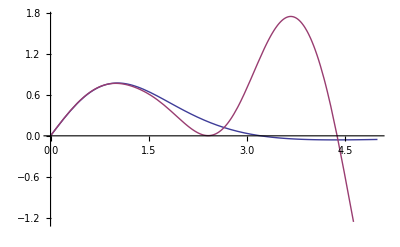

```mathematica
Plot[{2*4*NIntegrate[Im[ⅇ^(ⅈ *x* k)1/(k Sinh[k*π])k^4],{k,0,100}],Im[a0+a2+a3+a4+a5+a6]},{x,0,5}]
```